# Finding Hidden Structure in a NN (MNIST)

First, load the data and define the NetEncoder/NetDecoder

```mathematica
trainingData=ResourceData["MNIST","TrainingData"];
testData=ResourceData["MNIST","TestData"];
mnistEncoder=NetEncoder[{"Image",{28,28},"ColorSpace"->"Grayscale"}];
mnistDecoder=NetDecoder[{"Class",Range[0,9]}];
```

We’ll slightly modify the Neural Network from yesterday to see more examples.

```mathematica
uNet=NetChain[{
ConvolutionLayer[32,{3,3}],
Ramp,
PoolingLayer[{2,2},{2,2}],
ConvolutionLayer[64,{3,3}],
Ramp,
PoolingLayer[{2,2},{2,2}],
FlattenLayer[],
DropoutLayer[0.2],
LinearLayer[128],
Ramp,
LinearLayer[10],
SoftmaxLayer[]
},
"Input"->mnistEncoder,
"Output"->mnistDecoder];
```

The process of building a Network graph and training the Neural Network is similar.

```mathematica
iNet=NetInitialize[uNet];
tNet=NetGraph[<|"MyNet"->iNet,"loss"->CrossEntropyLossLayer["Index"]|>,{NetPort["Input"]->"MyNet"->NetPort["loss","Input"],NetPort["Target"]->NetPort["loss","Target"]}];

trainAssoc=<|"Input"->Keys[trainingData],"Target"->Values[trainingData]+1|>;
testAssoc=<|"Input"->Keys[testData],"Target"->Values[testData]+1|>;


results=NetTrain[tNet,trainAssoc,All,ValidationSet->testAssoc,MaxTrainingRounds->5]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:4690  rounds:5  time:1.8min  examples/s:2762
data | ,,  training examples:60000  validation examples:10000  processed examples:300160  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:2.42×10^-2  error:0.745%
validation | ,,  loss:2.96×10^-2  error:0.930%
 | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
tdNet=NetExtract[results["TrainedNet"],"MyNet"];
tdNet=NetReplacePart[tdNet,{"Input"->mnistEncoder,"Output"->mnistDecoder}];
```

```mathematica
%244
```

NetChain[<11>]

```mathematica
%37
```

NetChain[…]

## Measurements

ClassifierMeasurements performs a variety of statistical measurements on our trained Neural Network.

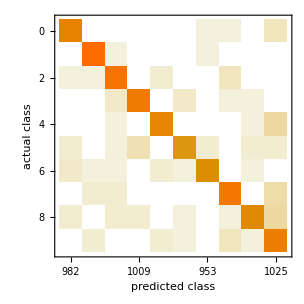
Classifier Measurements
Classifier method | Net
Number of test examples | 10000
Accuracy | (99.090.09) %
Accuracy baseline | (11.350.32) %
Geometric mean of probabilities | 0.97 ± 0.0031
Mean cross entropy | 0.0306 ± 0.0032
Single evaluation time | 4.85 ms/example
Batch evaluation speed | 5.78 examples/ms
-Graphics- |

```mathematica
measurements=ClassifierMeasurements[tdNet,testData]
```

```mathematica
measurements["Accuracy"]
measurements["WorstClassifiedExamples"]
```

0.9827

{-Graphics-→6,-Graphics-→0,-Graphics-→6,-Graphics-→9,-Graphics-→7,-Graphics-→6,-Graphics-→2,-Graphics-→7,-Graphics-→5,-Graphics-→0}

```mathematica
measurements["LeastCertainExamples"]
```

{-Graphics-→3,-Graphics-→9,-Graphics-→8,-Graphics-→9,-Graphics-→9,-Graphics-→3,-Graphics-→3,-Graphics-→7,-Graphics-→8,-Graphics-→2}

```mathematica
measurements["TopConfusions"]
```

{2→7,3→8,6→8,4→9,3→5,8→9,2→8,4→6,5→6,2→3}

## Finding Hidden Features

NetMeasurements can also plot the mean activation of the results after a certain number of layers. Here are the mean activations after the first convolutional layer with 6 channels.

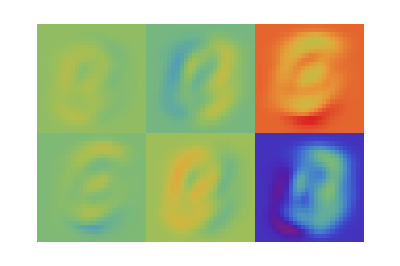

```mathematica
activations1=NetMeasurements[tdNet,testData,NetPort[{1,"Output"}]];
ArrayPlot[ArrayFlatten@Partition[activations1,3],ColorFunction->"Rainbow",FrameTicks->None]
```

Activations after the fourth layer. At this level the output is a convolution with three channels.

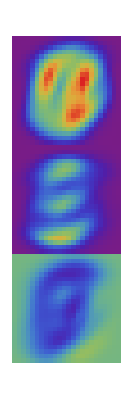

```mathematica
activations4=NetMeasurements[tdNet,testData,NetPort[{4,"Output"}]];
ArrayPlot[Flatten[activations4,1],ColorFunction->"Rainbow",FrameTicks->None]
```

```mathematica
tNet
```

NetGraph[<>]